## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW151012";

(*键名直接用短名，里面加上下划线*)
inspiralParams={};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dphi_0] does not exist.

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

```mathematica
CalculateSampleRatios[samples,{23,14},{23-5,14-5},{23+16,14+4}]
```

{<|p→dbeta_2,LowerBoundRatios→<|1→1.23058,2→1.03787|>,MedianRatios→<|1→1.52487,2→1.24308|>,UpperBoundRatios→<|1→1.60529,2→2.27453|>,WidthRatios→<|1→1.92648,2→3.51118|>|>,<|p→dbeta_3,LowerBoundRatios→<|1→1.53627,2→1.72415|>,MedianRatios→<|1→2.09305,2→2.25652|>,UpperBoundRatios→<|1→1.73484,2→2.41837|>,WidthRatios→<|1→1.90505,2→3.11259|>|>,<|p→dalpha_2,LowerBoundRatios→<|1→1.17831,2→1.2662|>,MedianRatios→<|1→1.13245,2→1.25527|>,UpperBoundRatios→<|1→1.01514,2→1.19724|>,WidthRatios→<|1→0.875273,2→1.12827|>|>,<|p→dalpha_3,LowerBoundRatios→<|1→1.18773,2→1.05108|>,MedianRatios→<|1→1.21123,2→1.14556|>,UpperBoundRatios→<|1→1.21002,2→1.1512|>,WidthRatios→<|1→1.22912,2→1.25132|>|>,<|p→dalpha_4,LowerBoundRatios→<|1→1.18991,2→1.33622|>,MedianRatios→<|1→1.14783,2→1.24897|>,UpperBoundRatios→<|1→0.989888,2→1.2056|>,WidthRatios→<|1→0.818444,2→1.07498|>|>}

## m1-m2 Plot, 22

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00205};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1.5]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,60}

输入q范围：{1,3}

m1范围：{11.487,122.86}

m2范围：{6.82558,68.9219}

对称数据：原始 60315 + 镜像 60315

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.968877 and 3.28404×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.968877（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.38954×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 122.86} × {6.82558, 122.86}

等高线值：{0.00205}，共 2 条

第一条前3点：{{19.664,19.3016},{19.6641,19.3015},{19.667,19.2984}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.359455

可信水平百分比：35.9455%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.359455

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
m1m2PDF[p][42,28]
```

0.00303946

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

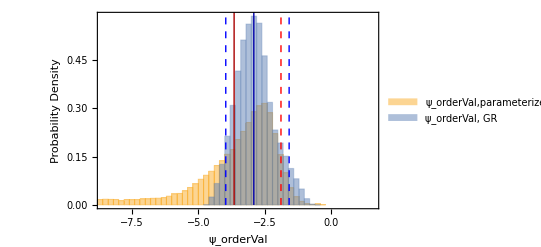

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
3931./2
```

1965.5

```mathematica
probability=prob;
probability=0.1965;
probability=0.1965;
(*probability=0.2;*)
PlotInversion[p,probability,10,40,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.40175, 0.59825}

实际使用的 GR 概率区间上下界: {-3.07597, -2.73961}

实际使用的 Param 概率区间上下界: {-4.31266, -3.18659}

GR下界: 点数=30 | Y>0点数=30 | 平均误差=1.0066×10^-15

GR上界: 点数=30 | Y>0点数=30 | 平均误差=1.46549×10^-15

Greater::nord: Invalid comparison with 3.58178+16.6184 ⅈ attempted.

Greater::nord: Invalid comparison with 3.76628+17.6016 ⅈ attempted.

Greater::nord: Invalid comparison with 3.97418+18.5797 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param下界: 点数=30 | Y>0点数=6 | 平均误差=0.248004

Param上界: 点数=30 | Y>0点数=30 | 平均误差=1.92291×10^-14

{{11,11.},{12,12.},{13,13.},{14,14.},{15,15.}}

{{11,10.9935},{12,11.993},{13,12.9924},{14,13.9918},{15,14.9912}}

chi1L取值：0.432612

chi2L取值：0.485378

=====================================================

-Graphics-

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 44009 + 镜像 44009

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999493 and 5.25173×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.999493（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.2544×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001}，共 2 条

第一条前3点：{{33.0494,33.7127},{33.0491,33.7131},{32.9071,33.8437}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.546954

可信水平百分比：54.6954%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.546954

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

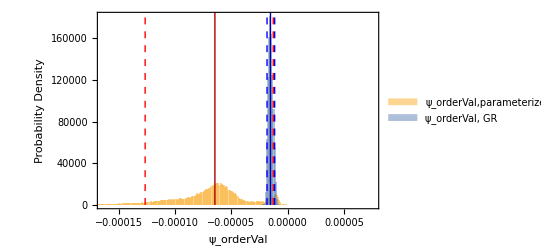

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.12895, 0.87105}

实际使用的 GR 概率区间上下界: {-0.000017519, -0.0000125638}

实际使用的 Param 概率区间上下界: {-0.00010356, -0.0000327105}

GR下界: 点数=570 | Y>0点数=0 | 平均误差=1.5866×10^-19

GR上界: 点数=570 | Y>0点数=570 | 平均误差=1.60693×10^-6

Param下界: 点数=570 | Y>0点数=0 | 平均误差=3.02697×10^-19

Param上界: 点数=570 | Y>0点数=570 | 平均误差=0.0000217536

{{3.1,-1.8874},{3.2,-1.94829},{3.3,-2.00917},{3.4,-2.07005},{3.5,-2.13094}}

{{3.1,3.23565},{3.2,3.34003},{3.3,3.44463},{3.4,3.5496},{3.5,3.65298}}

chi1L取值：0.169045

chi2L取值：0.106174

=====================================================

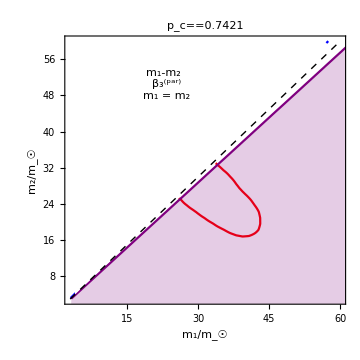

```mathematica
probability=prob;
probability=0.9343;
probability=0.7421;
(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,60,0.1,cm->True,cd->False,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.1,spinPercentile2->0.1,contourIndices->{2}]
```

## Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.007};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,80}

输入q范围：{1,5}

m1范围：{3.4461,217.926}

m2范围：{1.63444,91.8959}

对称数据：原始 3018 + 镜像 3018

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999998（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 217.926} × {1.63444, 217.926}

等高线值：{0.007}，共 2 条

第一条前3点：{{15.7381,16.414},{15.6538,16.5078},{15.6063,16.5609}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.380873

可信水平百分比：38.0873%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.380873

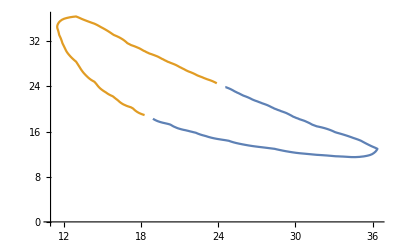

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

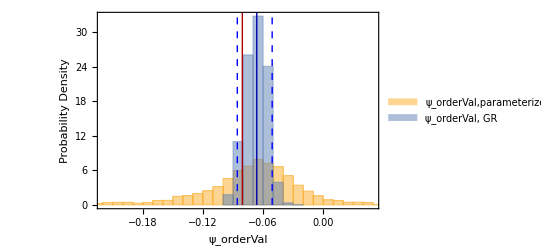

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.1664;
probability=0.1664;

PlotInversion[p,probability,3,40,0.2,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4168, 0.5832}

实际使用的 GR 概率区间上下界: {-0.0689782, -0.0637383}

实际使用的 Param 概率区间上下界: {-0.0960893, -0.0684981}

Greater::nord: Invalid comparison with 3.13477-0.642799 ⅈ attempted.

Greater::nord: Invalid comparison with 3.33055-0.683687 ⅈ attempted.

Greater::nord: Invalid comparison with 3.52612-0.725574 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=185 | Y>0点数=0 | 平均误差=0.000134999

GR上界: 点数=185 | Y>0点数=185 | 平均误差=2.60302×10^-17

Param下界: 点数=185 | Y>0点数=3 | 平均误差=0.000446374

Param上界: 点数=185 | Y>0点数=185 | 平均误差=3.05311×10^-17

{{3.2,3.2},{3.4,3.4},{3.6,3.6},{3.8,-2.02647-4.06398 ⅈ},{4.,-2.13313-4.27787 ⅈ}}

{{3.2,3.01867},{3.4,3.20733},{3.6,3.396},{3.8,3.58467},{4.,3.77333}}

chi1L取值：0.389408

chi2L取值：0.446755

=====================================================

-Graphics-

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,60},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0034};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,60}

输入q范围：{1,3}

m1范围：{3.4461,122.86}

m2范围：{2.04767,68.9219}

对称数据：原始 50496 + 镜像 50496

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 122.86} × {2.04767, 122.86}

等高线值：{0.0034}，共 4 条

第一条前3点：{{18.8044,19.1819},{18.6978,19.2759},{18.6818,19.2899}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.517528

可信水平百分比：51.7528%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.517528

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

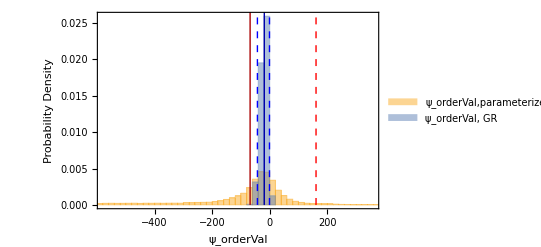

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.34185, 0.65815}

实际使用的 GR 概率区间上下界: {-23.5588, -13.9474}

实际使用的 Param 概率区间上下界: {-255.201, -25.5948}

GR下界: 点数=53 | Y>0点数=53 | 平均误差=2.68129×10^-14

GR上界: 点数=53 | Y>0点数=53 | 平均误差=2.95948×10^-14

Param下界: 点数=53 | Y>0点数=0 | 平均误差=1.18513×10^-13

Param上界: 点数=53 | Y>0点数=53 | 平均误差=5.90555×10^-14

{{8,-27.348},{9,-30.7665},{10,-34.185},{11,-37.6035},{12,-41.022}}

{{8,7.92032},{9,8.91036},{10,9.9004},{11,10.8904},{12,11.8805}}

chi1L取值：0.349223

chi2L取值：0.465364

=====================================================

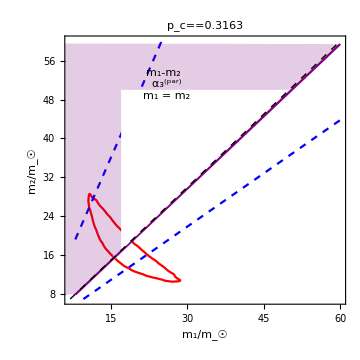

```mathematica
probability=prob;
(*probability=0.3843;*)
probability=0.3163;
(*probability=0.3843;*)

PlotInversion[p,probability,7,60,1,cm->True,cd->True,cu->False,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

```mathematica
jz
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,80}

输入q范围：{1,5}

m1范围：{3.4461,217.926}

m2范围：{1.63444,91.8959}

对称数据：原始 3029 + 镜像 3029

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999998（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 217.926} × {1.63444, 217.926}

等高线值：{0.005}，共 2 条

第一条前3点：{{19.5137,18.8378},{19.6629,18.6985},{19.7209,18.6322}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.536312

可信水平百分比：53.6312%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.536312

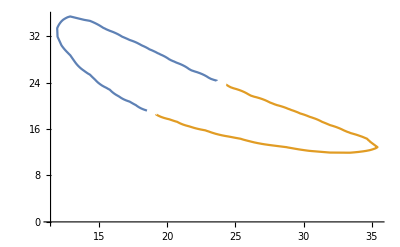

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

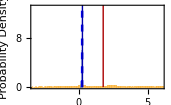

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
0.6623/2
```

0.33115

```mathematica
probability=prob;
probability=0.3312;
probability=0.3312;

PlotInversion[p,probability,3,40,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.3344, 0.6656}

实际使用的 GR 概率区间上下界: {0.248749, 0.265497}

实际使用的 Param 概率区间上下界: {0.268847, 2.57117}

GR下界: 点数=185 | Y>0点数=185 | 平均误差=4.69594×10^-17

GR上界: 点数=185 | Y>0点数=185 | 平均误差=4.5009×10^-17

Param下界: 点数=185 | Y>0点数=185 | 平均误差=6.24125×10^-17

Greater::nord: Invalid comparison with -2.28501-2.29507 ⅈ attempted.

Greater::nord: Invalid comparison with -2.37028-2.38071 ⅈ attempted.

Greater::nord: Invalid comparison with -2.50971-2.52075 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param上界: 点数=185 | Y>0点数=0 | 平均误差=8.11021×10^-16

{{3.2,3.44436},{3.4,3.65963},{3.6,3.8749},{3.8,4.09017},{4.,4.30544}}

{{3.2,-2.28501-2.29507 ⅈ},{3.4,-2.37028-2.38071 ⅈ},{3.6,-2.50971-2.52075 ⅈ},{3.8,-2.64913-2.66079 ⅈ},{4.,-2.78856-2.80083 ⅈ}}

chi1L取值：0.379905

chi2L取值：0.462829

=====================================================

-Graphics-

# utils